# Michelson Interferometry

## Using CGS units instead of SI, LISA parameters for the laser and arm lengths, and Smetana relations for the index of refraction of electrons.

56.3367 √ne

4.8032×10^-10

1

9.1094×10^-28

30000000000

133/1250000

(75000000000000000 π)/133

1-8.95762×10^-13 ne

2.5×10^10

2.5×10^10 (1-8.95762×10^-13 ne)

2.5×10^10-2.5×10^10 (1-8.95762×10^-13 ne)

2500000/133 (2.5×10^10-2.5×10^10 (1-8.95762×10^-13 ne)) π

Cos[1250000/133 (2.5×10^10-2.5×10^10 (1-8.95762×10^-13 ne)) π]^2

Cos[29526.2467442649740457015355571381850018530958587885885429975995517651917884042199119176205389296717 (2.5×10^10-2.5×10^10 (1.-8.9576188665531762200491142063098868480487679821777646793634630739688873291015625×10^-13 ne))]^2

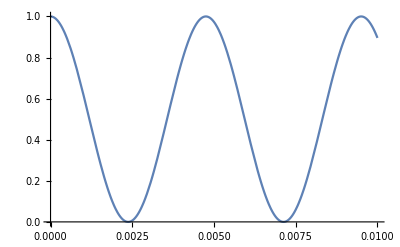

```mathematica
omegap=Sqrt[(ne*(e^2))/(enot*me)]
e=4.8032*10^(-10)
enot=1
me=9.1094*10^(-28)
vlight=3*10^10
lambda=1064*10^-7
omega=(2*Pi*vlight)/lambda
indexref=1-0.5*((omegap^2)/omega)
armL1=2.5*10^10
armL2=(2.5*10^10)*indexref
opdiff=armL1-armL2
del=(opdiff/lambda)*2*Pi
Intens=(Cos[del/2])^(2)
Intens=SetPrecision[Intens,100]
Plot[Intens,{ne,0,0.01},WorkingPrecision->100]
```

Used CGS units instead of SI. enot (permeativity of space) was set arbitrarily to 1 as stated in this article: britannica.com/science/permittivity 
not sure if that is right.